```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

```mathematica
countryname="United States"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years];
nop = (Length[data]-4)/2;
isolates = data[[2;;Length[data]-3;;2]];
resistance = data[[3;;Length[data]-3;;2]];
rfreq =resistance/isolates;
carbcons = data[[-3]]/10000;
conbreak = data[[-2,1;;nop]];
cardiv =Table[carbcons*conbreak[[i]],{i,1,nop}];
pc =  data[[-1,1]]; (*proportion of carbapanem prescription out of all antibiotics prescribed for bacterial pneuomonia NOTE: Update with better estimate.*)
tc = cardiv/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
prop = cardiv/tc;
diff = tc-cardiv;
```

```mathematica
r[t_,r0_,a_,nn_] := ⅇ^((a)* Total[cn[[1;;t]]]+((theta-1)*nn)*t)/((1/r0)-1+ⅇ^((a)* Total[cn[[1;;t]]]+((theta-1)*nn)*t)) ;
```

```mathematica
thetarand=RandomVariate[BetaDistribution[240,4],10]
ssize=Length[thetarand];
```

{0.954212,0.979295,0.996097,0.986397,0.989584,0.973259,0.966021,0.992125,0.988618,0.976227}

```mathematica
Lik[r0_,a_,nn_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,a,nn]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,a,nn]],{j,1,tt}]]
```

```mathematica
max  = PadRight[{},ssize,Null];
fr0 = max; fa=max; fnn=max;
For[i=1,i≤ssize,i++,{iso=isolates[[1]],resis = resistance[[1]],cn = cardiv[[1]],df =diff[[1]],theta=thetarand[[i]],{max[[i]],{fr0[[i]],fa[[i]],fnn[[i]]}}=NMaximize[{Lik[r0,a,nn],0< r0< 1, nn>0},{r0,a,nn}, MaxIterations->100000]}]
max
mfr0 = Table[fr0[[i]][[2]],{i,1,ssize}] 
mfa = Table[fa[[i]][[2]],{i,1,ssize}]
mfnn = Table[fnn[[i]][[2]],{i,1,ssize}]
```

{-158.072,-158.072,-158.072,-158.072,-158.072,-158.072,-158.072,-158.072,-158.072,-158.072}

{0.00205465,0.00205465,0.00205465,0.00205465,0.00205465,0.00205465,0.00205465,0.00205465,0.00205465,0.00205465}

{243.107,243.107,243.107,243.107,243.107,243.107,243.107,243.107,243.107,243.107}

{3.25574×10^-11,7.15285×10^-11,3.48276×10^-10,0.,0.,5.37404×10^-11,2.86986×10^-41,-1.50269×10^-16,0.,6.00567×10^-11}

```mathematica
t=Range[1,tt]; 
res = Transpose@{years,rfreq[[1]]};(*resistance frequency data*)
x  = PadRight[{},ssize,Null];
For[i=1,i≤ssize,i++,{iso=isolates[[1]],resis = resistance[[1]],cn = cardiv[[1]],df =diff[[1]],theta=thetarand[[i]],x[[i]] = Table[r[j,mfr0[[i]],mfa[[i]],mfnn[[i]]],{j,1,tt}]}];
fit =  Table[Transpose@{years,x[[i]]},{i,1,ssize}];
```

```mathematica
plotD = ListPlot[{res},PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,PlotLegends->{"Resistance frequency"},PlotLabel->"United States (K.P.)"];
plotM = Table[ListLinePlot[{fit[[i]]},PlotStyle->{{Orange,Thick}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States (KP)",PlotLegends->{"Model fit"}],{i,1,ssize}];
```

```mathematica
Table[Show[plotD,plotM[[i]]],{i,1,ssize}];
```

```mathematica
tcI = cardivSQ/pc;
curcarb = carbcons[[-1]];  (*current carbapenem consumption*)
py =2020; (*projection till year py*) 
npy = py -years[[-1]];
pyears = Range[ years[[-1]],py];

(*Status Quo consumtions*)
projSQ =ConstantArray[curcarb,Round[npy]];  (*maintaining current carbapenem consumption levels*) 
carbconSQ = Join[carbcons,projSQ];
cardivSQ =carbconSQ*conbreak[[1]];
tcSQ = cardivSQ/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
diffSQ = tcSQ-cardivSQ;
(*Intervention consumtions*)
intv = 0.01; (*reducing current carbapenem consumption by (1-intv) % in next npy years linearly*)
projI = Range[curcarb,intv*curcarb,curcarb*(intv-1)/(npy-1)];
carbconI = Join[carbcons,projI];
cardivI =carbconI*conbreak[[1]];
tcI = cardivSQ/pc; (*Total antibiotics prescribed for bacterial pneumonia.*)
diffI = tcI-cardivI;
(*Status Quo resistances*)
y  = PadRight[{},ssize,Null];
For[i=1,i≤ssize,i++,{iso=isolates[[1]],resis = resistance[[1]],cn = cardivSQ,df =diffSQ[[1]],theta=thetarand[[i]],y[[i]] = Table[r[j,mfr0[[i]],mfa[[i]],mfnn[[i]]],{j,tt,tt+npy}]}];
prrSQ =  Table[Transpose@{pyears,y[[i]]},{i,1,ssize}];
(*Intervention resistances*)
z  = PadRight[{},ssize,Null];
For[i=1,i≤ssize,i++,{iso=isolates[[1]],resis = resistance[[1]],cn = cardivI,df =diffI[[1]],theta=thetarand[[i]],z[[i]] = Table[r[j,mfr0[[i]],mfa[[i]],mfnn[[i]]],{j,tt,tt+npy}]}];
prrI =  Table[Transpose@{pyears,z[[i]]},{i,1,ssize}];
y;
z;
```

```mathematica
plotPSQ = Table[ListLinePlot[{prrSQ[[i]]},PlotStyle->{{Orange,Thick,Dashed}},PlotStyle->Gray,AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Status Quo projection"}],{i,1,ssize}];
plotPI = Table[ListLinePlot[{prrI[[i]]},PlotStyle->{{Gray,Thick,Dashed}},AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Intervention projection"}],{i,1,ssize}];
```

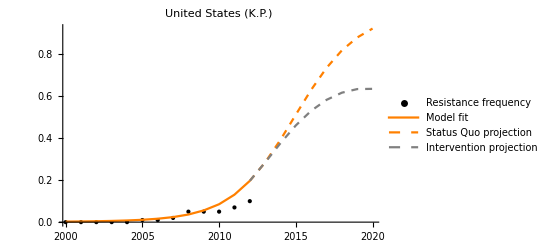
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[plotD,plotM[[i]],plotPSQ[[i]],plotPI[[i]],PlotRange-> All],{i,1,ssize}]
```